```mathematica
Graph[{AL<->FL,AL<->GA,AL<->MS,AL<->TN,AR<->LA,AR<->MO,AR<->MS,AR<->OK,AR<->TN,AR<->TX,AZ<->CA,AZ<->NM,AZ<->NV,AZ<->UT,CA<->NV,CA<->OR,CO<->KS,CO<->NE,CO<->NM,CO<->OK,CO<->UT,CO<->WY,CT<->MA,CT<->NY,CT<->RI,DC<->MD,DC<->VA,DE<->MD,DE<->NJ,DE<->PA,FL<->GA,GA<->NC,GA<->SC,GA<->TN,IA<->IL,IA<->MN,IA<->MO,IA<->NE,IA<->SD,IA<->WI,ID<->MT,ID<->NV,ID<->OR,ID<->UT,ID<->WA,ID<->WY,IL<->IN,IL<->KY,IL<->MO,IL<->WI,IN<->KY,IN<->MI,IN<->OH,KS<->MO,KS<->NE,KS<->OK,KY<->MO,KY<->OH,KY<->TN,KY<->VA,KY<->WV,LA<->MS,LA<->TX,MA<->NH,MA<->NY,MA<->RI,MA<->VT,MD<->PA,MD<->VA,MD<->WV,ME<->NH,MI<->OH,MI<->WI,MN<->ND,MN<->SD,MN<->WI,MO<->NE,MO<->OK,MO<->TN,MS<->TN,MT<->ND,MT<->SD,MT<->WY,NC<->SC,NC<->TN,NC<->VA,ND<->SD,NE<->SD,NE<->WY,NH<->VT,NJ<->NY,NJ<->PA,NM<->OK,NM<->TX,NV<->OR,NV<->UT,NY<->PA,NY<->VT,OH<->PA,OH<->WV,OK<->TX,OR<->WA,PA<->WV,SD<->WY,TN<->VA,UT<->WY,VA<->WV},VertexLabels->"Name", PlotTheme->"Detailed", ImageSize->Full,GraphHighlight->{FL<->GA<->TN<->VA<->WV}]
```

```mathematica
Graph[{AL<->FL,AL<->GA,AL<->MS,AL<->TN,AR<->LA,AR<->MO,AR<->MS,AR<->OK,AR<->TN,AR<->TX,AZ<->CA,AZ<->NM,AZ<->NV,AZ<->UT,CA<->NV,CA<->OR,CO<->KS,CO<->NE,CO<->NM,CO<->OK,CO<->UT,CO<->WY,CT<->MA,CT<->NY,CT<->RI,DC<->MD,DC<->VA,DE<->MD,DE<->NJ,DE<->PA,FL<->GA,GA<->NC,GA<->SC,GA<->TN,IA<->IL,IA<->MN,IA<->MO,IA<->NE,IA<->SD,IA<->WI,ID<->MT,ID<->NV,ID<->OR,ID<->UT,ID<->WA,ID<->WY,IL<->IN,IL<->KY,IL<->MO,IL<->WI,IN<->KY,IN<->MI,IN<->OH,KS<->MO,KS<->NE,KS<->OK,KY<->MO,KY<->OH,KY<->TN,KY<->VA,KY<->WV,LA<->MS,LA<->TX,MA<->NH,MA<->NY,MA<->RI,MA<->VT,MD<->PA,MD<->VA,MD<->WV,ME<->NH,MI<->OH,MI<->WI,MN<->ND,MN<->SD,MN<->WI,MO<->NE,MO<->OK,MO<->TN,MS<->TN,MT<->ND,MT<->SD,MT<->WY,NC<->SC,NC<->TN,NC<->VA,ND<->SD,NE<->SD,NE<->WY,NH<->VT,NJ<->NY,NJ<->PA,NM<->OK,NM<->TX,NV<->OR,NV<->UT,NY<->PA,NY<->VT,OH<->PA,OH<->WV,OK<->TX,OR<->WA,PA<->WV,SD<->WY,TN<->VA,UT<->WY,VA<->WV},VertexLabels->"Name",PlotTheme->"Detailed",ImageSize->Full,GraphHighlight->{FL<->GA,GA<->TN,TN<->VA,VA<->WV}]
```

-Graphics-

```mathematica
Graph[{AL->FL,AL->GA,AL->MS,AL->TN,AR->LA,AR->MO,AR->MS,AR->OK,AR->TN,AR->TX,AZ->CA,AZ->NM,AZ->NV,AZ->UT,CA->NV,CA->OR,CO->KS,CO->NE,CO->NM,CO->OK,CO->UT,CO->WY,CT->MA,CT->NY,CT->RI,DC->MD,DC->VA,DE->MD,DE->NJ,DE->PA,FL->GA,GA->NC,GA->SC,GA->TN,IA->IL,IA->MN,IA->MO,IA->NE,IA->SD,IA->WI,ID->MT,ID->NV,ID->OR,ID->UT,ID->WA,ID->WY,IL->IN,IL->KY,IL->MO,IL->WI,IN->KY,IN->MI,IN->OH,KS->MO,KS->NE,KS->OK,KY->MO,KY->OH,KY->TN,KY->VA,KY->WV,LA->MS,LA->TX,MA->NH,MA->NY,MA->RI,MA->VT,MD->PA,MD->VA,MD->WV,ME->NH,MI->OH,MI->WI,MN->ND,MN->SD,MN->WI,MO->NE,MO->OK,MO->TN,MS->TN,MT->ND,MT->SD,MT->WY,NC->SC,NC->TN,NC->VA,ND->SD,NE->SD,NE->WY,NH->VT,NJ->NY,NJ->PA,NM->OK,NM->TX,NV->OR,NV->UT,NY->PA,NY->VT,OH->PA,OH->WV,OK->TX,OR->WA,PA->WV,SD->WY,TN->VA,UT->WY,VA->WV},VertexLabels->"Name", PlotTheme->"Detailed", ImageSize->Full]
```

-Graphics-

```mathematica
iMatrix = {{1,0,1,0,0,0,0},
		{1,1,0,0,0,0,0},
		{0,1,1,1,0,0,0},
		{0,0,0,1,1,1,0},
		{0,0,0,0,1,0,1},
		{0,0,0,0,0,1,1}};
```

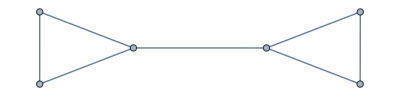

```mathematica
IncidenceGraph[iMatrix]
```

```mathematica
aMatrix={{0,1,1,0,0,0},
		{1,0,1,0,0,0},
		{1,1,0,1,0,0},
		{0,0,1,0,1,1},
		{0,0,0,1,0,1},
		{0,0,0,1,1,0}};
```

```mathematica
AdjacencyGraph[aMatrix]
```

-Graphics-